```mathematica
Norm1=sqrt((125/2)(sqrt(Pi)/2));
gauss1[x]:=Exp[-(x-400)^2/(125^2)]/Norm1;
```

```mathematica
Integrate[gauss1[x]*gauss1[x],{x,0,1000}]
```

(4 √2 (Erf[(16 √2)/5]+Erf[(24 √2)/5]))/(125 π^(3/2) sqrt^4)

```mathematica
125/2 √(π/2) (Erf[(16 √2)/5]+Erf[(24 √2)/5])
```

125/2 √(π/2) (Erf[(16 √2)/5]+Erf[(24 √2)/5])

```mathematica
Nsolve[Integrate[gauss1[x]*gauss1[x],{x,0,1000}]]
```

Nsolve[(4 √2 (Erf[(16 √2)/5]+Erf[(24 √2)/5]))/(125 π^(3/2) sqrt^4)]

```mathematica
Integrate[Exp[-(x-400)^2/(125^2)]/Norm1,{x,0,1000}]
```

(4 (Erf[16/5]+Erf[24/5]))/(125 √π)

```mathematica
Plot[gauss1[x],{x,0,1000}]
```

-Graphics-

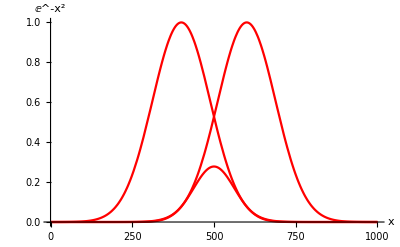

```mathematica
Plot[{Exp[-(x-400)^2/(125^2)],Exp[-(x-600)^2/(125^2)],Exp[-(x-400)^2/(125^2)]*Exp[-(x-600)^2/(125^2)]},{x,0,1000},
PlotStyle->Red,
PlotRange->All,
AxesLabel->TraditionalForm/@{x,Exp[-x^2]}]
```

```mathematica
gauss1[2]
```

gauss1[2]

```mathematica
Manipulate[Plot[gauss1(x),{x,0.,1000.}],{gauss1,0.,1.}]
```

```mathematica
Manipulate[Plot[gauss1 x,{x,0.,1000.}],{gauss1,0.,0.01}]
```

```mathematica
Manipulate[Plot[gauss x,{x,-8,8}],{gauss,-8,8}]
```

```mathematica
Exp[-(x-400)^2/(125^2)]*Exp[-(x-600)^2/(125^2)]
```

ⅇ^(-(-600+x)^2/15625-(-400+x)^2/15625)

```mathematica
Simplify[ⅇ^(-(-600+x)^2/15625-(-400+x)^2/15625)]
```

ⅇ^(-(2 (260000-1000 x+x^2))/15625)

```mathematica
∫ⅇ^(-(2 (260000-1000 x+x^2))/15625)ⅆx
```

(125 √(π/2) Erf[1/125 √2 (-500+x)])/(2 ⅇ^(32/25))

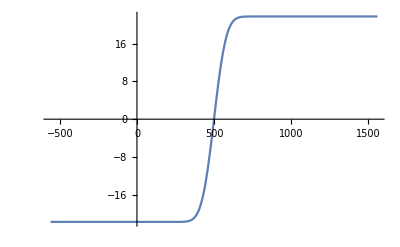

```mathematica
Plot[(125 √(π/2) Erf[1/125 √2 (-500+x)])/(2 ⅇ^(32/25)),{x,-560.6601717798212,1560.6601717798212}]
```